### Start choosing the example:

```mathematica
t=13;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,0,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.269248 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.340387,Null}

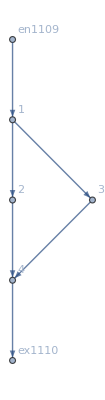

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→95.,u1140→95.,u1141→55.,u1142→55.,u1143→15.,u1144→95.,u1145→55.,u1146→55.,u1147→15.,u1148→15.,u1149→15.,u1150→95.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.38023×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.38023×10^-16

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→19.6805,u1140→19.6805,u1141→17.3402,u1142→17.3402,u1143→15.,u1144→19.6805,u1145→17.3402,u1146→17.3402,u1147→15.,u1148→15.,u1149→15.,u1150→19.6805|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.54409×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.54409×10^-17

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→20.5515,u1140→20.5515,u1141→17.7758,u1142→17.7758,u1143→15.,u1144→20.5515,u1145→17.7758,u1146→17.7758,u1147→15.,u1148→15.,u1149→15.,u1150→20.5515|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→23.1887,u1140→23.1887,u1141→19.0944,u1142→19.0944,u1143→15.,u1144→23.1887,u1145→19.0944,u1146→19.0944,u1147→15.,u1148→15.,u1149→15.,u1150→23.1887|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.35438×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.35438×10^-16

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→65.0434,u1140→65.0434,u1141→40.0217,u1142→40.0217,u1143→15.,u1144→65.0434,u1145→40.0217,u1146→40.0217,u1147→15.,u1148→15.,u1149→15.,u1150→65.0434|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[8.52651×10^-14,ComplexInfinity]

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→95.,u1140→95.,u1141→55.,u1142→55.,u1143→15.,u1144→95.,u1145→55.,u1146→55.,u1147→15.,u1148→15.,u1149→15.,u1150→95.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→286.7,u1140→286.7,u1141→150.85,u1142→150.85,u1143→15.,u1144→286.7,u1145→150.85,u1146→150.85,u1147→15.,u1148→15.,u1149→15.,u1150→286.7|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→7208.19,u1140→7208.19,u1141→3611.59,u1142→3611.59,u1143→15.,u1144→7208.19,u1145→3611.59,u1146→3611.59,u1147→15.,u1148→15.,u1149→15.,u1150→7208.19|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→2.99468×10^14,u1140→2.99468×10^14,u1141→1.49734×10^14,u1142→1.49734×10^14,u1143→15.,u1144→2.99468×10^14,u1145→1.49734×10^14,u1146→1.49734×10^14,u1147→15.,u1148→15.,u1149→15.,u1150→2.99468×10^14|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.707107

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.707107

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

<|j1111→40.,j1112→40.,j1113→40.,j1114→40.,j1115→80.,j1116→80.,j1117→0.,j1118→0.,j1119→0.,j1120→0.,j1121→0.,j1122→0.,jt1123→0.,jt1124→0.,jt1125→0.,jt1126→0.,jt1127→40.,jt1128→40.,jt1129→40.,jt1130→0.,jt1131→40.,jt1132→0.,jt1133→0.,jt1134→40.,jt1135→0.,jt1136→40.,jt1137→0.,jt1138→0.,u1139→95.,u1140→95.,u1141→55.,u1142→55.,u1143→15.,u1144→95.,u1145→55.,u1146→55.,u1147→15.,u1148→15.,u1149→15.,u1150→95.|>